## SaveCellzillaModel Example File

LGPL License applies.
See http://xlr8r.info and http://cellzilla.info for more information.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (0.15-α (19-Jun-09)) loaded Sat 20 Jun 2009 15:19:16 using xlr8r 0.74 (13 May 2009)

```mathematica
<<xlr8r.m
```

```mathematica
<<CelleratorML.m
```

Generate a Cellzilla Model from Random Centers and convert the centers to a Tissue object

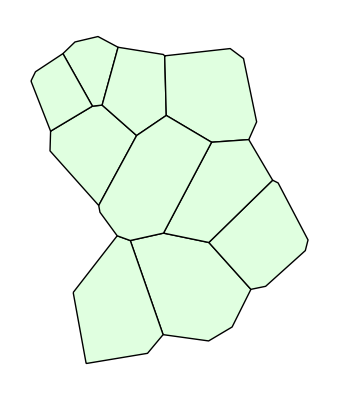

```mathematica
n=10; 
r:= RandomReal[{0, 10}]; 
centers=Table[{r,r}, {n}];
w=BoundedCellVoronoi[centers];
ShowTissue[w]
```

Define a Cellerator Model and save it to the xml file ring.xml

```mathematica
reactions={{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XP, X],MM[K,v,K,v]},
{Underoverscript[Z⟺ZP, YP, Y],MM[K,v,K,v]}};
cic= {X-> 1, Y-> 2, Z-> 3};
cparms={v-> 1, K-> .5};
```

```mathematica
SaveModel["ring.xml" , reactions, "InitialConditions"-> cic, "Parameters"-> cparms]
```

ring.xml

Define the Cellzilla Network on this template

```mathematica
bignet=CelleratorNetwork[reactions, {{X, DX}, {Y, DY}, {Z, DZ}}, w];
```

10 Cells.

6 internal reactions in each cell.

60 intracellular reactions.

102 diffusion reactions.

162 total reactions.

Define Random Initial Conditions

```mathematica
myic=ListICToCellzillaIC[{X-> Table[RandomReal[{0,3}], {n}], Y-> Table[RandomReal[{0,3}], {n}], Z-> Table[RandomReal[{0,3}], {n}], XP-> Table[0, {n}], YP-> Table[0, {n}], ZP-> Table[0, {n}]}];
```

Generate the Symbolic XML using CellzillaModelToSXML

```mathematica
SaveCellzillaModel["example.xml",
"Models"-> {"ring.xml"},
"Tissue"-> w, 
"Parameters"-> {DX-> 9, DY-> 10, DZ-> 11},
"InitialConditions"-> myic,
"DiffusingSpecies"-> {{X,DX}, {Y,DY}, {Z,DZ}}]
```

Model name: CellzillaModel

Model file name(s) or URL(s):

ring.xml

3 Diffusing Species

3 Parameters

60 Initial Conditions

2-D tissue: 38 vertices; 47 edges; 10 cells.

example.xml